```mathematica
solarSail={
Fn->p*A*Abs[Cos[α[t]]]*Cos[α[t]]*(1+ϵ),
Ft->p*A*(1-ϵ)*Abs[Cos[α[t]]]*Sin[α[t]]
}
```

{Fn→A p (1+ϵ) Abs[Cos[α[t]]] Cos[α[t]],Ft→A p (1-ϵ) Abs[Cos[α[t]]] Sin[α[t]]}

```mathematica
normalAndTangentForces={
Fr->Fn*Cos[α[t]-θ[t]]-Ft*Sin[α[t]-θ[t]],
Fs->Fn*Sin[α[t]-θ[t]]+Ft*Cos[α[t]-θ[t]]
}
```

{Fr→Fn Cos[α[t]-θ[t]]-Ft Sin[α[t]-θ[t]],Fs→Ft Cos[α[t]-θ[t]]+Fn Sin[α[t]-θ[t]]}

```mathematica
generalEquations={
D[r[t],t]==vr[t],
D[θ[t],t]==vs[t]/r[t],
D[vs[t],t]==(-vr[t]*vs[t])/r[t]+Fr/m,
D[vr[t],t]==vs[t]^2/r[t]-μ/r[t]^2+Fr/m
}
```

{r'[t]==vr[t],θ'[t]==vs[t]/r[t],vs'[t]==Fr/m-(vr[t] vs[t])/r[t],vr'[t]==Fr/m-μ/r[t]^2+vs[t]^2/r[t]}

```mathematica
solarSailEquations=generalEquations/.normalAndTangentForces/.solarSail//FullSimplify;
```

```mathematica
solarSailEquations//TableForm
```

vr[t]==r'[t]
θ'[t]==vs[t]/r[t]
(A p Abs[Cos[α[t]]] (Cos[2 α[t]-θ[t]]+ϵ Cos[θ[t]]))/m==(vr[t] vs[t])/r[t]+vs'[t]
μ/r[t]+r[t] vr'[t]==(A p Abs[Cos[α[t]]] (Cos[2 α[t]-θ[t]]+ϵ Cos[θ[t]]) r[t])/m+vs[t]^2

```mathematica
(*State functions: θ[t], r[t], vs[t], vr[t]*)
(*Control function: α[t]*)
(*Constants: A p m μ ϵ*)
```

```mathematica
constants={
A->1(*m.b2*),
p->1 (*Momentum flux of incoming light per unit area (THINK!)*),
m->1 (*kg*),
μ->3.986004418*10^14 (*m.b3/s.b2*),
ϵ->1,
r0->7000*10^3};
```

```mathematica
circularInitialConditions={
θ[0]==0,
r[0]==r0,
vs[0]==Sqrt[μ/r0],
vr[0]==0
};
```

```mathematica
tend=20000;
```

```mathematica
sol=NDSolve[
Join[Append[solarSailEquations,α[t]==π/2], circularInitialConditions]/.constants,
{θ[t],r[t],vs[t],vr[t],α[t]},
{t,0,tend}
]
```

{{θ[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],vs[t]→InterpolatingFunction[…][t],vr[t]→InterpolatingFunction[…][t],α[t]→InterpolatingFunction[…][t]}}

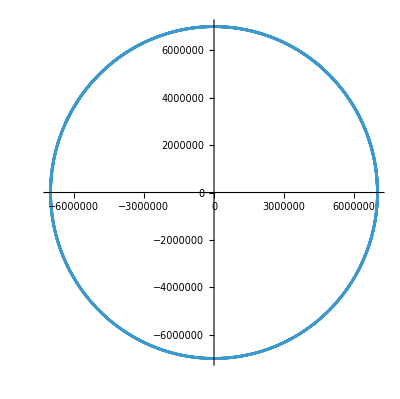

```mathematica
ParametricPlot[{r[t]*Cos[θ[t]],r[t]*Sin[θ[t]]}/.sol, {t,0,tend}]
```